#### initial cell

```mathematica
SetDirectory[NotebookDirectory[]];
plotrange = {0,1300000};
VMPlot[vm_] := ListLinePlot[vmᵀ[[{3,5,7}]],PlotRange->plotrange]
```

#### 1-2 ;mono;50M~400M ---dirty

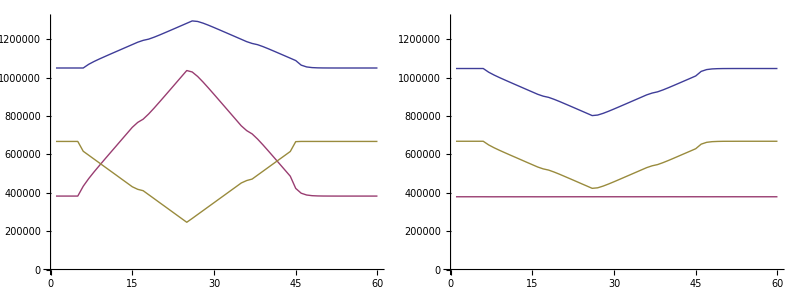

```mathematica
vm6 = Import["../dataset/1-2_mono_50M~400M/8.log"][[4;;]];
vm7 = Import["../dataset/1-2_mono_50M~400M/9.log"][[4;;]];
{{VMPlot[vm6],VMPlot[vm7]}}//TableForm
```

#### 1-2;mono;5VM;50M~400M

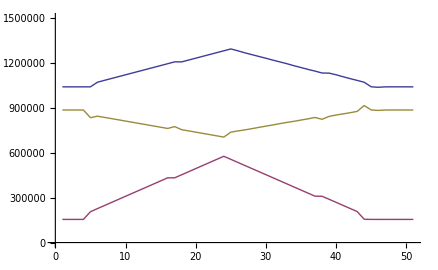
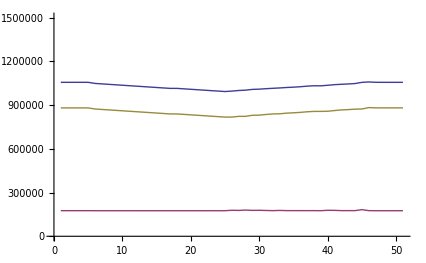
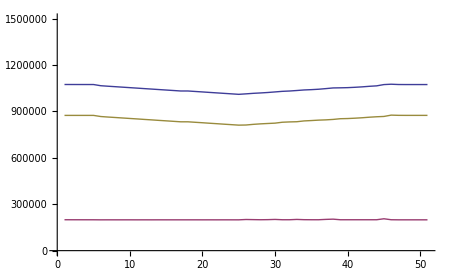
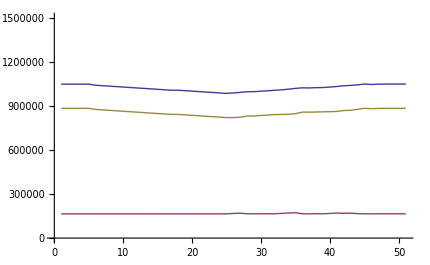
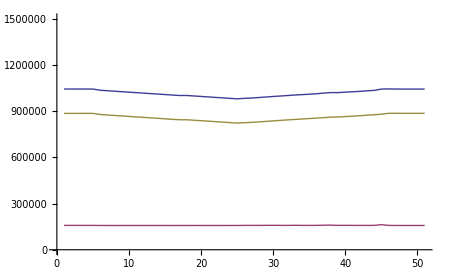
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- |

```mathematica
vm1 = Import["../dataset/1-4_mono_5VM/8.log"][[4;;]];
vm2 = Import["../dataset/1-4_mono_5VM/9.log"][[4;;]];
vm3 = Import["../dataset/1-4_mono_5VM/10.log"][[4;;]];
vm4 = Import["../dataset/1-4_mono_5VM/11.log"][[4;;]];
vm5 = Import["../dataset/1-4_mono_5VM/12.log"][[4;;]];
plotrange = {0,1500000};
{{VMPlot[vm1],VMPlot[vm2]},{VMPlot[vm3],VMPlot[vm4]},{VMPlot[vm5]}}//TableForm
```